```mathematica
(*Partial Trace Code*)
(*system, subsystem(s) being traced out, dimensions of subsystems*)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
dTraceSystem[D_, s_, dimen_]:=Module[{Qudits,TrkM,dim,z,q,n,M,k,p,j,b,i,c,perm}, (

Qudits=Reverse[Sort[s]];
TrkM=D;
dim=dimen;

z=(Dimensions[Qudits][[1]]+1);

For[q=1,q<z,q++,
n=Log[dim,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qudits[[q]];
If[k==n,
TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
 ],

For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<dim^n+1,i++,
If[IntegerDigits[i-1,dim,n][[n]]≠IntegerDigits[i-1,dim,n][[n-j-1]] && Count[b, i]  ==0, 
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)];
c=Range[dim^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,dim, n]),{n},{n-j-1}],dim]+1)}];
M=M[[perm,perm]];
 ]    
];
   ];

TrkM={};
For[p=1,p<dim^n+1,p=p+dim,
TrkM=Append[TrkM,∑_(h=0)^(dim-1) Take[M[[p+h,All]],{1+h,dim^n,dim}]];
]
]
]

;Return[TrkM])
]
```

```mathematica
(*Defining basic variables*)

zero = {{1} , {0}};
one = {{0} , {1}};

ϕplus =( KroneckerProduct[zero , zero]+KroneckerProduct[one , one])/Sqrt[2];
ϕminus = ( KroneckerProduct[zero , zero]-KroneckerProduct[one , one])/Sqrt[2];
ψplus = ( KroneckerProduct[zero , one]+KroneckerProduct[one , zero])/Sqrt[2];
ψminus = ( KroneckerProduct[zero , one]-KroneckerProduct[one , zero])/Sqrt[2];

Φplus = ϕplus.ConjugateTranspose[ϕplus];
Φminus = ϕminus.ConjugateTranspose[ϕminus];
Ψplus = ψplus.ConjugateTranspose[ψplus];
Ψminus = ψminus.ConjugateTranspose[ψminus];

(*Defining vector r which builds up 2 chains of entangled memory pairs and performs a BSM, entangling only the first and last memory, this vector outputs the values of the new weightings of our BSM*)

r[p__,q__]:=
{(p[[4]] q[[1]] + p[[3]] q[[2]] + p[[2]] q[[3]] + p[[1]] q[[4]]) , (p[[3]] q[[1]] + p[[4]] q[[2]] + p[[1]] q[[3]] + p[[2]] q[[4]]),
(p[[2]] q[[1]] + p[[1]] q[[2]] + p[[4]] q[[3]] + p[[3]] q[[4]]), (p[[1]] q[[1]] + p[[2]] q[[2]] + p[[3]] q[[3]] + p[[4]] q[[4]])
}

(*Creating a function that iteratively repeats this procedure for n memory-memory chains so that we can entangle the first and last memory of n pairs and perform an analysis on the quality of the state produced*)

rNtimes[p__,n_]:=If[n==1,r[p,p],r[rNtimes[p,n-1],p]]
```

```mathematica
(*Defining the error functions*)

(*Standard Gaussian*)
f[x_, μ_ , σ_]:=Exp[-(x - μ)^2 / (2 * σ^2)]/(σ * Sqrt[2 π]);
(*probability of correctly interpreting the measurement outcome*)
Pc[σ_ ?NumericQ, ν_?NumericQ]:= NIntegrate[f[x , 0 , σ] , {x , -0.5 * Sqrt[π] + ν , 0.5 * Sqrt[π] - ν}]
(*probability for making a logical error*)
Pf[σ_?NumericQ , ν_?NumericQ]:= 2 * NIntegrate[f[x , 0 , σ] , {x , 0.5 * Sqrt[π] + ν , 1.5 * Sqrt[π] - ν}]

(*State after post-selected dual-homodyne measurement which is heralded with success probability (Pc+Pf)^2*)

(*Defining the new probabilties corresponding to the errors*)

p1[σ_ , ν_]:= Pc[σ ,ν]^2/(Pc[σ , ν] + Pf[σ , ν])^2
p2[σ_ , ν_]:= Pc[σ , ν] * Pf[σ , ν]/(Pc[σ , ν] + Pf[σ , ν])^2
p3[σ_ , ν_]:= Pf[σ , ν] ^ 2/(Pc[σ , ν] + Pf[σ , ν])^2

(*Re-Defining the Bell State Mixture in terms of parameters {σ,ν}*)
ρBellStateMixture[σ_ , ν_]:=p1[σ , ν] Φplus + p2[σ , ν] (Φminus + Ψplus) + p3[σ , ν] Ψminus
```

```mathematica
(*Performing the linear map on our set of vectors which depend on {σ , ν}*)
newvector[σ_ , ν_]:= {p1[σ , ν] , p2[σ , ν] , p2[σ , ν] , p3[σ , ν]}

(*Feeding in my new vector into my iterative function that makes n chains*)
chainfunction[σ_ , ν_]:=rNtimes[newvector[σ,ν],1000]
```

```mathematica
(*Building up a table of all possible vectors for the Bell State Mixture in terms of parameters {σ , ν}*)
tab=Table[chainfunction[σ,ν],{σ,0.1,1,0.01},{ν,0,0.5*Sqrt[π],0.01}]
```

```mathematica
(*10,000 2U entangled memory pairs*)
longerchainfunction[σ_ , ν_]:=rNtimes[chainfunction[σ , ν] , 10]
tab2 = Table[longerchainfunction[σ,ν],{σ,0.1,1,0.01},{ν,0,0.5*Sqrt[π],0.01}]
```

```mathematica
(*100,000 2U entangled memory pairs*)
evenlongerchainfunction[σ_ , ν_]:=rNtimes[longerchainfunction[σ , ν] , 10]
tab3 = Table[evenlongerchainfunction[σ,ν],{σ,0.1,1,0.01},{ν,0,0.5*Sqrt[π],0.01}]
```

```mathematica
(*1,000,000 2U entangled memory pairs*)
muchlongerchainfunction[σ_ , ν_]:=rNtimes[evenlongerchainfunction[σ , ν] , 10]
tab4 = Table[muchlongerchainfunction[σ,ν],{σ,0.1,1,0.01},{ν,0,0.5*Sqrt[π],0.01}]
```

```mathematica
(*10,000,000 2U entangled memory pairs*)
evenmuchlongerchainfunction[σ_ , ν_]:=rNtimes[muchlongerchainfunction[σ , ν] , 10]
tab5= Table[evenmuchlongerchainfunction[σ,ν],{σ,0.1,1,0.01},{ν,0,0.5*Sqrt[π],0.01}]
```

```mathematica
Dynamic[σ]
Dynamic[ν]
```

```mathematica
(*Now I want to perform an analysis on these states by inspecting the fidelity with respect to the Φplus Bell state and the hashing rate for each state*)

(*Fidelity*)
fidelity[ρ_ , σ_]:=Tr[MatrixPower[MatrixPower[ρ , 0.5].σ.MatrixPower[ρ , 0.5] , 0.5]] ^ 2

(*Distllable entanglement*)

(*Von Neumann entropy*)
vonneumann[mat_]:=-Eigenvalues[mat].Log2[Eigenvalues[mat] + 10^-16]//N
(*Hashing bound*)
hashingbound[mat_]:=Max[vonneumann[dTraceSystem[mat , {2} , 2]] - vonneumann[mat] , vonneumann[dTraceSystem[mat , {1} , 2]] - vonneumann[mat]]
(*Hashing rate*)
hashingrate[mat_]:=Re[hashingbound[mat] *( Tr[mat])]
```

```mathematica
(*Fidelity*)
fidelitytable=Table[fidelity[Φplus , tab[[i , j]][[1]] Φplus + tab[[i , j]][[2]] Φminus + tab[[i , j]][[3]] Ψplus + tab[[i , j]][[4]] Ψminus],{i , 1 , 91} , {j , 1 , 89}];

(*Distillable Entanglement*)
hashingratetable = Table[Max[0 , hashingrate[tab[[i , j]][[1]] Φplus + tab[[i , j]][[2]] Φminus + tab[[i , j]][[3]] Ψplus + tab[[i , j]][[4]] Ψminus]],{i , 1 , 91} , {j , 1 , 89}];
```

```mathematica
σvalues = Table[σ , {σ , 0 , 1 , 0.01}];
νvalues = Table[ν , {ν , 0 , 0.5 Sqrt[π] , 0.01}];
```

```mathematica
(*Probability of success*)
probtab1 = Table[((Pc[σ , ν] + Pf[σ , ν])^2 )^1000, {σ , 0.1 , 1 , 0.01} , {ν , 0 , 0.5*Sqrt[π] , 0.01}];
```

General::munfl: 0.44101^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.373884^1000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.307028^1000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
0.99^1000
0.98^1000
0.8^1000
```

0.0000431712

1.68297×10^-9

1.23023×10^-97

```mathematica
(*Entanglement Rate*)
entanglementrate1000 = Table[probtab1[[i , j]] * hashingratetable[[i , j]] , {i , 1 , 91} , {j , 1 , 89}]
```

```mathematica
(*Set γ = 0.5 , Pd = 0 , Vis = 1*)
SingleRailState[η_,γ_,Pd_,Vis_]:=2*{{(1-Pd) Pd γ^2,0,0,0},{0,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,0},{0,1/2 (1-Pd)^2 (1-γ) γ √η*Vis,(1-Pd) Pd (1-γ) γ (1-√η)+1/2 (1-Pd)^2 (1-γ) γ √η,0},{0,0,0,(1-Pd) Pd (1-γ)^2 (1-√η)^2+(1-Pd)^2 (1-γ)^2 (1-√η) √η}}
```

```mathematica
(*Set Pd = 0 , Vis = 1*)
DualRailState[η_,Pd_,Vis_]:=4*{{1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η,0,0,0},{0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,1/16 (1-Pd)^4 η*Vis^2,0},{0,1/16 (1-Pd)^4 η*Vis^2,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η+1/16 (1-Pd)^4 η,0},{0,0,0,1/4 (1-Pd)^2 Pd^2 (1-√η)^2+1/4 (1-Pd)^3 Pd (1-√η) √η}}
```

```mathematica
ComposedState = SingleRailState[η , 0.5 , 0 , 1]//MatrixForm
```

(0. | 0 | 0 | 0
0 | 2 (0.+0.125 √η) | 0.25 √η | 0
0 | 0.25 √η | 2 (0.+0.125 √η) | 0
0 | 0 | 0 | 2 (0.+0.25 (1-√η) √η))

```mathematica
(*This is not Bell diagonal so we feed it into the code for the BSM map*)

(*CNOT*)
CNOT = {{1 , 0 , 0 , 0} , {0 , 1 , 0 , 0} , {0 , 0 , 0 , 1} , {0 , 0 , 1 , 0}};
(*Application of CNOT to qubits 2 and 3*)
GATE1 = KroneckerProduct[IdentityMatrix[2] , CNOT , IdentityMatrix[2]];
(*Applying a Hadamard gate to qubit 2*)
GATE2 = KroneckerProduct[IdentityMatrix[2] , HadamardMatrix[2] , IdentityMatrix[4]];
(*Post selectively project qubits 2 and 3 onto state |0>, i.e., performing a measurement in the Pauli Z basis*)
PROJ = KroneckerProduct[IdentityMatrix[2] , zero.ConjugateTranspose[zero] , zero.ConjugateTranspose[zero] , IdentityMatrix[2]];

(*Defining all possible state vector basis elements for 4 qubits*)
StateVectors = ArrayReshape[Table[{i1 , i2 , i3 , i4} , {i1 , 0 , 1} , {i2 , 0 , 1} , {i3 , 0 , 1} , {i4 , 0 , 1}] , {16 , 4}];
(*Post-Selectively filtering all basis elements to consider the case when qubits 2 and 3 are both 0*)
Patt00 = {};
Do[If[StateVectors[[i , 2 ;; 3]] === {0 , 0} , AppendTo[Patt00 , i];] , {i , 1 , Length[StateVectors]}]

(*Applying a BSM to qubits 2 and 3*)
postBSMstate = PROJ.GATE2.GATE1.ComposedState.ConjugateTranspose[GATE1].ConjugateTranspose[GATE2].ConjugateTranspose[PROJ];
(*Post-Selectively measuring outcome |0> after a Puali-Z measurement on qubits 2 and 3*)
PostSelectedState = postBSMstate[[Patt00 , Patt00]];

(*Diagonalising the pair of memories in the Bell measurement basis - this allows us to find the weighting of each Bell state for the Bell diagonal state of our memories*)
DiagonalisedPostSelectedState = Eigenvectors[PostSelectedState].PostSelectedState.ConjugateTranspose[Eigenvectors[PostSelectedState]]//FullSimplify;
```

Part::partw: Part {1,2,9,10} of (0. | 0 | 0 | 0
0 | 2 (0.+0.125 √η) | 0.25 √η | 0
0 | 0.25 √η | 2 (0.+0.125 √η) | 0
0 | 0 | 0 | 2 (0.+0.25 (1+Times[«2»]) √η)) does not exist.

```mathematica
(*10,000 2U Memory Qubit Pairs*)

(*Fidelity*)
fidelitytable2=Table[fidelity[Φplus , tab2[[i , j]][[1]] Φplus + tab2[[i , j]][[2]] Φminus + tab2[[i , j]][[3]] Ψplus + tab2[[i , j]][[4]] Ψminus],{i , 1 , 91} , {j , 1 , 89}];

(*Distillable Entanglement*)
hashingratetable2 = Table[Max[0 , hashingrate[tab2[[i , j]][[1]] Φplus + tab2[[i , j]][[2]] Φminus + tab2[[i , j]][[3]] Ψplus + tab2[[i , j]][[4]] Ψminus]],{i , 1 , 91} , {j , 1 , 89}];
```

```mathematica
(*100,000 2U Entangled Memory pairs*)
(*Fidelity*)
fidelitytable3=Table[fidelity[Φplus , tab3[[i , j]][[1]] Φplus + tab3[[i , j]][[2]] Φminus + tab3[[i , j]][[3]] Ψplus + tab3[[i , j]][[4]] Ψminus],{i , 1 , 91} , {j , 1 , 89}];

(*Distillable Entanglement*)
hashingratetable3 = Table[Max[0 , hashingrate[tab3[[i , j]][[1]] Φplus + tab3[[i , j]][[2]] Φminus + tab3[[i , j]][[3]] Ψplus + tab3[[i , j]][[4]] Ψminus]],{i , 1 , 91} , {j , 1 , 89}];
```

```mathematica
(*1,000,000 2U Entangled Memory pairs*)
(*Fidelity*)
fidelitytable4=Table[fidelity[Φplus , tab4[[i , j]][[1]] Φplus + tab4[[i , j]][[2]] Φminus + tab4[[i , j]][[3]] Ψplus + tab4[[i , j]][[4]] Ψminus],{i , 1 , 91} , {j , 1 , 89}];

(*Distillable Entanglement*)
hashingratetable4 = Table[Max[0 , hashingrate[tab4[[i , j]][[1]] Φplus + tab4[[i , j]][[2]] Φminus + tab4[[i , j]][[3]] Ψplus + tab4[[i , j]][[4]] Ψminus]],{i , 1 , 91} , {j , 1 , 89}];
```

```mathematica
(*10,000,000 2U Entangled Memory pairs*)
(*Fidelity*)
fidelitytable5=Table[fidelity[Φplus , tab5[[i , j]][[1]] Φplus + tab5[[i , j]][[2]] Φminus + tab5[[i , j]][[3]] Ψplus + tab5[[i , j]][[4]] Ψminus],{i , 1 , 91} , {j , 1 , 89}];

(*Distillable Entanglement*)
hashingratetable5 = Table[Max[0 , hashingrate[tab5[[i , j]][[1]] Φplus + tab5[[i , j]][[2]] Φminus + tab5[[i , j]][[3]] Ψplus + tab5[[i , j]][[4]] Ψminus]],{i , 1 , 91} , {j , 1 , 89}];
```

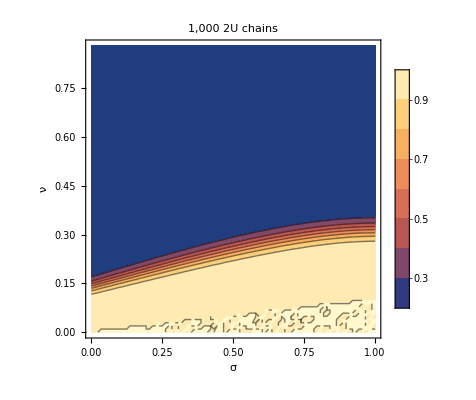
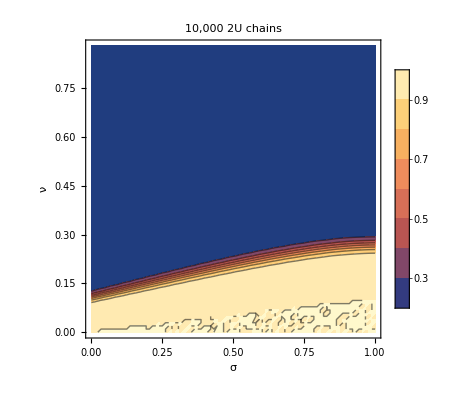
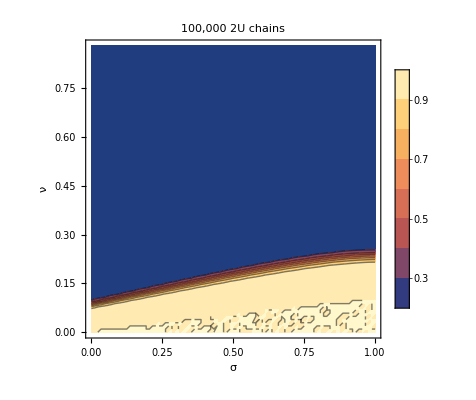
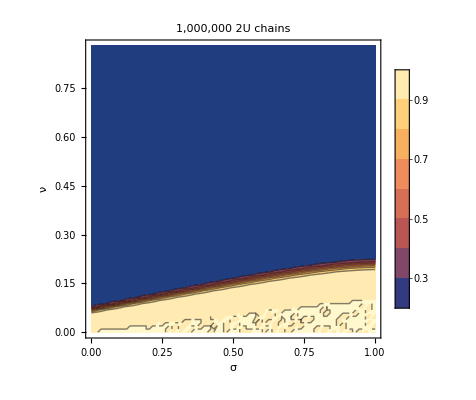
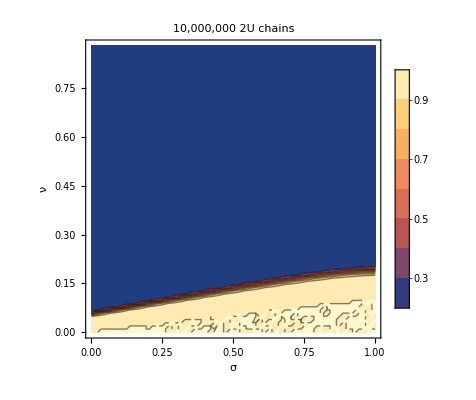

```mathematica
{ListContourPlot[fidelitytable,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000 2U chains"],ListContourPlot[fidelitytable2,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000 2U chains"],ListContourPlot[fidelitytable3,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"100,000 2U chains"],ListContourPlot[fidelitytable4,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000,000 2U chains"],ListContourPlot[fidelitytable5,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000,000 2U chains"]}
```

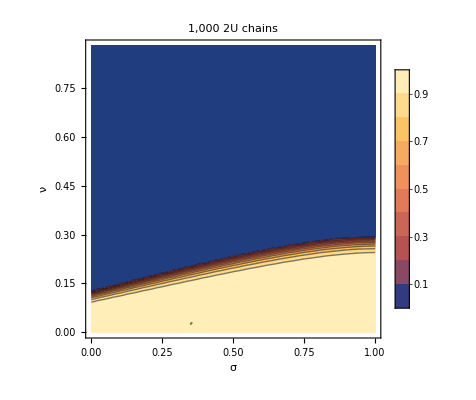
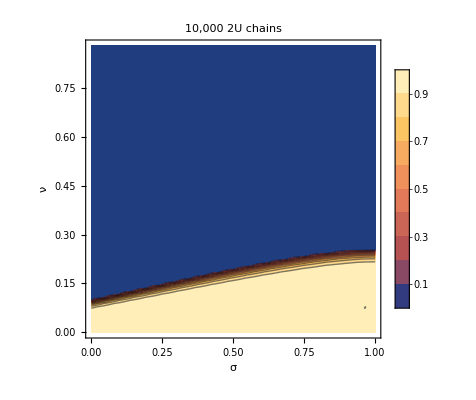
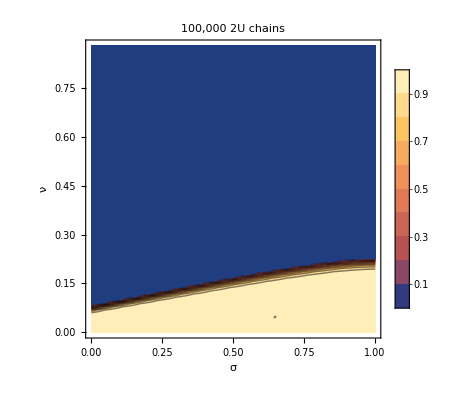
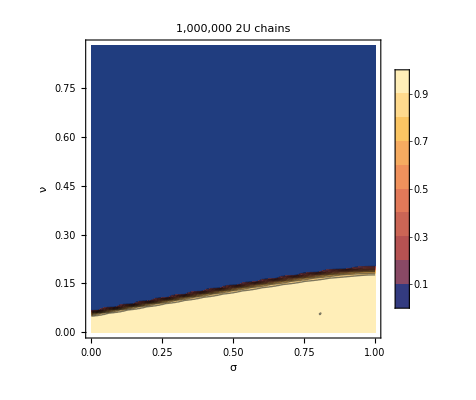
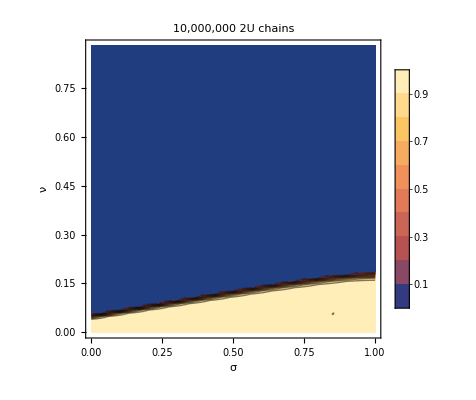

```mathematica
{ListContourPlot[hashingratetable,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000 2U chains"],ListContourPlot[hashingratetable2,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000 2U chains"],ListContourPlot[hashingratetable3,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"100,000 2U chains"],ListContourPlot[hashingratetable4,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000,000 2U chains"],ListContourPlot[hashingratetable5,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000,000 2U chains"]}
```

```mathematica
efcontour1 = ListContourPlot[fidelitytable,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000 2U chains"];

efcontour2 = ListContourPlot[fidelitytable2,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000 2U chains"];

efcontour3 = ListContourPlot[fidelitytable3,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"100,000 2U chains"];

efcontour4 = ListContourPlot[fidelitytable4,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000,000 2U chains"];

efcontour5 = ListContourPlot[fidelitytable5,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000,000 2U chains"];

(*Creating a GIF code*)
Export["entanglement_fidelity.gif" , {efcontour1 , efcontour2 , efcontour3 , efcontour4 , efcontour5} , "DisplayDurations" -> 0.5]
```

entanglement_fidelity.gif

```mathematica
hrcontour1 = ListContourPlot[hashingratetable,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000 2U chains"];

hrcontour2 = ListContourPlot[hashingratetable2,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000 2U chains"];

hrcontour3 = ListContourPlot[hashingratetable3,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"100,000 2U chains"];

hrcontour4 = ListContourPlot[hashingratetable4,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"1,000,000 2U chains"];

hrcontour5 = ListContourPlot[hashingratetable5,FrameLabel->{σ,ν},LabelStyle->Directive[Bold,18],
PlotLegends->Automatic,PlotRange->All, DataRange-> {{Min[σvalues] , Max[σvalues]} , {Min[νvalues] , Max[νvalues]}} , PlotLabel->"10,000,000 2U chains"];

Export["hashing_rate.gif" , {hrcontour1 , hrcontour2 , hrcontour3 , hrcontour4 , hrcontour5} , "DisplayDurations" -> 0.5]
```

hashing_rate.gif